# Linear protocol and counterdiabatic driving in STIRAP

The boundary conditions of the reference protocol are not important and, the peaks in the reference protocols are much bigger than the boundary conditions. 
 Time-rescalling: realizar as simulações, mas lembrar que depende muito do protocolo escolhido para rescalonamento
 Unitary transform: ver artigo e realizar as contas.
 Santos and Sarandy. Realizei um procedimento de regularização e obtive os protocolos. Porém, esses protocolos são razoáveis? E qual a motivação teórica na literatura para regularização? 
 Questions: 1) what is the exact form of the eigenvalues of the counterdiabatic Hamiltonian? In this case, the FQ protocol is equal to the minimal time-averaged excess work protocol? 
Tarefas. Escrever resultados, formatar os gráficos, calcular os custos e investigar as questões acima.

```mathematica
ℏ = 1
Ωpi = 0.1
Ωpf = 10
ti = 0
Ωs[t_]:= 1.0
Ωp[t_, tf_]:=(Ωpf-Ωpi)*t/(tf-ti) + Ωpi
Δ = 0.1 
dΩp[t_,tf_]:=D[Ωp[b,tf],b]/.b-> t
dΩs[t_]:=D[Ωs[b],b]/.b-> t
Ωa[t_,tf_]:=2*(dΩp[t,tf]*Ωs[t]-Ωp[t,tf]*dΩs[t])/(Ωp[t,tf]^2 + Ωs[t]^2)
```

1

0.1

10

0

0.1

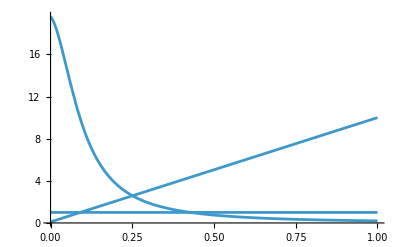

```mathematica
Show[Plot[Ωp[t,1.0],{t,ti,1.0}, PlotRange->All],
Plot[Ωs[t],{t,ti,1.0}],
Plot[Ωa[t,1.0],{t,ti,1.0}, PlotRange->All]]
```

```mathematica
(*Autovalores*)
(*Show[Plot[0.5*Sqrt[Ωp[t,tf]^2 + Ωs[t]^2], {t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Orange], Dashing[0.01]},FrameLabel ->{"t (μs)", "Eigenenergies / (ℏΩ_0)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_+(t)",10]},LegendLayout->"Row"],{Right,0.94}]],Plot[-0.5*Sqrt[Ωp[t,tf]^2 + Ωs[t]^2], {t,ti,tf},PlotRange->{-11,11},PlotTheme-> "Detailed",PlotStyle-> {Darker[Purple], DotDashed},FrameLabel ->{"t (μs)", "E_+(t)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_-(t)",10]},LegendLayout->"Row"],{Right,0.86}]], Plot[0,{t,ti,tf}, PlotRange->{-11,11},PlotTheme-> "Detailed",PlotStyle-> Darker[Magenta],FrameLabel ->{"t (μs)", "E_+(t)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_0(t)",10]},LegendLayout->"Row"],{Right,0.78}]]]*)
```

```mathematica
time= Table[tf/2.198,{tf,Tmin,Tmax, ΔT}]
time2 =  Table[tf/2.198,{tf,Tmin,Tmax-4*ΔT, ΔT}]
```

Table::iterb: Iterator {tf,Tmin,Tmax,ΔT} does not have appropriate bounds.

Table[tf/2.198,{tf,Tmin,Tmax,ΔT}]

Table::iterb: Iterator {tf,Tmin,Tmax-4 ΔT,ΔT} does not have appropriate bounds.

Table[tf/2.198,{tf,Tmin,Tmax-4 ΔT,ΔT}]

```mathematica
Δ= 0.1
tf = 9.0
Tmin = 0.1
Tmax = 100
m = 9
ΔT = (Tmax-Tmin)/m
Sol = Table[NDSolve[{ⅈ*ℏ*c1'[t] ==(ℏ/2)*Ωp[t,tf]*c2[t],ⅈ*ℏ*c2'[t] ==(ℏ/2)*Ωp[t,tf]*c1[t]+(ℏ/2)*Δ*c2[t]+ (ℏ/2)*Ωs[t]*c3[t],ⅈ*ℏ*c3'[t] ==+(ℏ/2)*Ωs[t]*c2[t],c1[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ],c2[ti]==0,c3[ti]==-Ωp[ti,tf]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ] },{c1,c2,c3},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
SolCD = Table[NDSolve[{ⅈ*ℏ*c1CD'[t] ==(ℏ/2)*Ωp[t,tf]*c2CD[t]+ⅈ*(ℏ/2)*Ωa[t,tf]*c3CD[t],ⅈ*ℏ*c2CD'[t] ==(ℏ/2)*Ωp[t,tf]*c1CD[t]+(ℏ/2)*Δ*c2CD[t]+(ℏ/2)*Ωs[t]*c3CD[t],ⅈ*ℏ*c3CD'[t] ==-ⅈ*(ℏ/2)*Ωa[t,tf]*c1CD[t]+(ℏ/2)*Ωs[t]*c2CD[t],c1CD[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ],c2CD[ti]==0,c3CD[ti]==-Ωp[ti,tf]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ] },{c1CD,c2CD,c3CD},{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

0.1

9.

0.1

100

9

11.1

{{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}}}

{{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}}}

```mathematica
(*Probabilities |1 >*)
p1 = Table[Abs[c1[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
p2 = Table[Abs[c2[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
p3 = Table[Abs[c3[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pCD1 = Table[Abs[c1CD[t]/.Part[Flatten[Part[SolCD,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pCD2 = Table[Abs[c2CD[t]/.Part[Flatten[Part[SolCD,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pCD3 = Table[Abs[c3CD[t]/.Part[Flatten[Part[SolCD,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
```

{0.929907,0.372193,0.204554,0.00211636,0.0219079,0.10104,0.104504,0.0446412,0.0213702,0.0251801}

{0.0593618,0.112802,0.224921,0.24218,0.151785,0.0424904,0.000391703,0.0229252,0.0488444,0.0390973}

{0.0107307,0.515003,0.570525,0.755704,0.826308,0.85647,0.895105,0.932435,0.929787,0.935724}

{0.00990098,0.00990098,0.00990099,0.00990098,0.00990098,0.00990099,0.00990099,0.00990099,0.00990099,0.00990099}

{6.91131×10^-18,2.09979×10^-15,5.52397×10^-15,8.73549×10^-17,9.46846×10^-17,1.36062×10^-16,3.95733×10^-16,7.24773×10^-17,2.03277×10^-16,2.3939×10^-17}

{0.990099,0.990099,0.990099,0.990099,0.990099,0.990099,0.990099,0.990099,0.990099,0.990099}

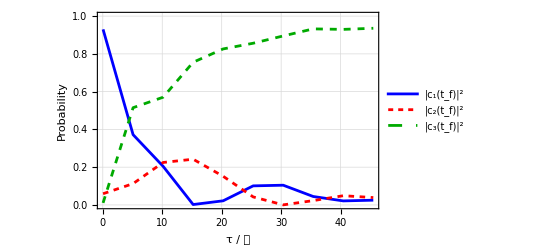

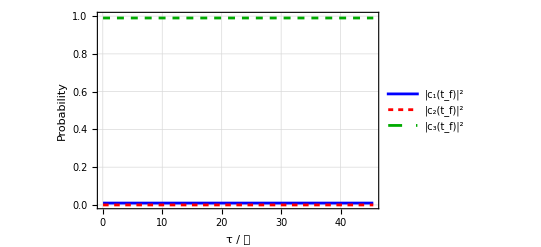

```mathematica
gLIN = Show[ListPlot[Transpose[{time,p1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,p2}], PlotStyle->{Red, Dashing[0.01]}, Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,p3}], PlotStyle->{Darker[Green], Dashed}, Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
gCD = Show[ListPlot[Transpose[{time,pCD1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,pCD2}], PlotStyle->{Red, Dashing[0.01]}, Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,pCD3}], PlotStyle->{Darker[Green], Dashed}, Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
```

## Reference protocol

```mathematica
Ω0 = 42506.6114781728
Ωpref[t_,tf_]:= Ω0*Exp[-(t-tf/2-tf/10)^2/(tf/6)^2]
Ωsref[t_,tf_]:= Ω0*Exp[-(t-tf/2+tf/10)^2/(tf/6)^2]
```

42506.6

## Minimal action

```mathematica
ProtMA = Table[NDSolve[{D[ΩpMA'[t]/(ΩpMA[t]^2 + Ωs[t]^2),t] + 4*Δ/(ΩpMA[t]^2 + Ωs[t]^2)^(3/2)*(ΩpMA''[t] - 2.5*ΩpMA[t]*ΩpMA'[t]^2/(ΩpMA[t]^2 + Ωs[t]^2)) ==0 , ΩpMA[ti]==Ωpi, ΩpMA[tf]==Ωpf},ΩpMA,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}}}

```mathematica
SolMA = Table[NDSolve[{ⅈ*ℏ*c1MA'[t] ==(ℏ/2)*Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]]*c2MA[t],ⅈ*ℏ*c2MA'[t] ==(ℏ/2)*Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]]*c1MA[t]+(ℏ/2)*Δ*c2MA[t]+ (ℏ/2)*Ωs[t]*c3MA[t],ⅈ*ℏ*c3MA'[t] ==+(ℏ/2)*Ωs[t]*c2MA[t],c1MA[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωpi^2 ],c2MA[ti]==0,c3MA[ti]==-Ωpi/Sqrt[Ωs[ti]^2 + Ωpi^2 ] },{c1MA,c2MA,c3MA},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}}}

```mathematica
pMA1 = Table[Abs[c1MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pMA2 = Table[Abs[c2MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pMA3 = Table[Abs[c3MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
```

{0.984324,0.0107227,0.00323732,0.0133057,0.0182923,0.0106757,0.0103394,0.0133311,0.0107533,0.00697127}

{0.00561012,0.0140692,0.00633096,0.00670444,0.000139075,0.00154227,0.00103779,0.0000810316,0.000729687,0.00012012}

{0.0100656,0.975209,0.990431,0.97999,0.981568,0.987782,0.988623,0.986588,0.988517,0.992908}

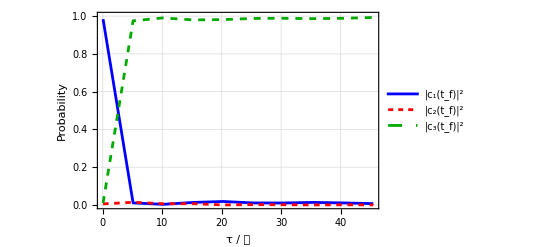

```mathematica
gMA = Show[ListPlot[Transpose[{time,pMA1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,pMA2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,pMA3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
```

## Fast quasidiabatic

```mathematica
ProtFQ = Table[NDSolve[{D[ΩpFQ'[t]/(ΩpFQ[t]^2 + Ωs[t]^2)^(3/2)*(1+1.5*Δ/(ΩpFQ[t]^2 + Ωs[t]^2)^(1/2)),t] ==0 , ΩpFQ[ti]==Ωpi, ΩpFQ[tf]==Ωpf},ΩpFQ,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}}}

```mathematica
SolFQ = Table[NDSolve[{ⅈ*ℏ*c1FQ'[t] ==(ℏ/2)*Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]]*c2FQ[t],ⅈ*ℏ*c2FQ'[t] ==(ℏ/2)*Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]]*c1FQ[t]+(ℏ/2)*Δ*c2FQ[t]+ (ℏ/2)*Ωs[t]*c3FQ[t],ⅈ*ℏ*c3FQ'[t] ==+(ℏ/2)*Ωs[t]*c2FQ[t],c1FQ[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωpi^2 ],c2FQ[ti]==0,c3FQ[ti]==-Ωpi/Sqrt[Ωs[ti]^2 + Ωpi^2 ] },{c1FQ,c2FQ,c3FQ},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}}}

```mathematica
pFQ1 = Table[Abs[c1FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pFQ2 = Table[Abs[c2FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pFQ3 = Table[Abs[c3FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
```

{0.988126,0.0459626,0.00320004,0.0101895,0.0140207,0.0098961,0.00948236,0.00909464,0.0124408,0.00954368}

{0.00187438,0.0701052,0.0135159,0.00199748,0.00317591,0.00173687,0.00168048,0.000505305,0.000380384,0.00123236}

{0.00999996,0.883931,0.983284,0.987813,0.982803,0.988367,0.988837,0.9904,0.987179,0.989224}

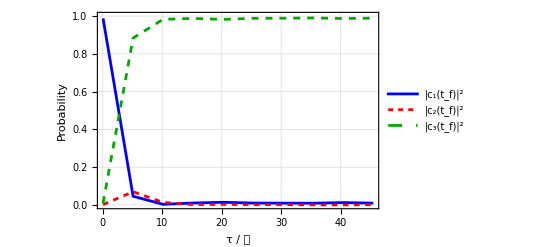

```mathematica
gFQ = Show[ListPlot[Transpose[{time,pFQ1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,pFQ2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,pFQ3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
```

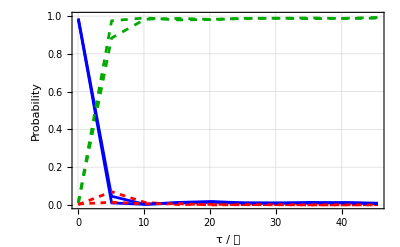

```mathematica
Show[gFQ,gMA]
```

## Boundary cancellation method

```mathematica
ΩpBCM[t_,tf_]:= Ωpi + ( Ωpf- Ωpi)*(3*((t-ti)/(tf-ti))^2 - 2*((t-ti)/(tf-ti))^3)
```

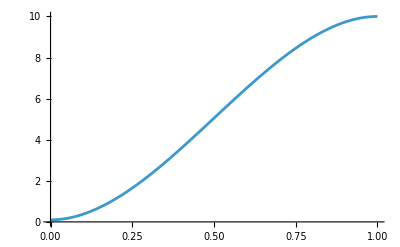

```mathematica
Plot[ΩpBCM[t,1.0],{t,ti,1.0}]
```

```mathematica
SolBCM = Table[NDSolve[{ⅈ*ℏ*c1BCM'[t] ==(ℏ/2)*ΩpBCM[t,tf]*c2BCM[t],ⅈ*ℏ*c2BCM'[t] ==(ℏ/2)*ΩpBCM[t,tf]*c1BCM[t]+(ℏ/2)*Δ*c2BCM[t]+ (ℏ/2)*Ωs[t]*c3BCM[t],ⅈ*ℏ*c3BCM'[t] ==+(ℏ/2)*Ωs[t]*c2BCM[t],c1BCM[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωpi^2 ],c2BCM[ti]==0,c3BCM[ti]==-Ωpi/Sqrt[Ωs[ti]^2 + Ωpi^2 ] },{c1BCM,c2BCM,c3BCM},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}}}

```mathematica
pBCM1 = Table[Abs[c1BCM[t]/.Part[Flatten[Part[SolBCM,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pBCM2 = Table[Abs[c2BCM[t]/.Part[Flatten[Part[SolBCM,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pBCM3 = Table[Abs[c3BCM[t]/.Part[Flatten[Part[SolBCM,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
```

{0.929983,0.382586,0.228104,0.00787321,0.0124828,0.0192743,0.0161918,0.0101139,0.00803851,0.0140313}

{0.0593705,0.0465127,0.0838835,0.0815308,0.0414159,0.00862818,0.000189909,0.0013192,0.000879265,0.0000301364}

{0.0106462,0.570901,0.688013,0.910597,0.946102,0.972098,0.983618,0.988566,0.991082,0.985938}

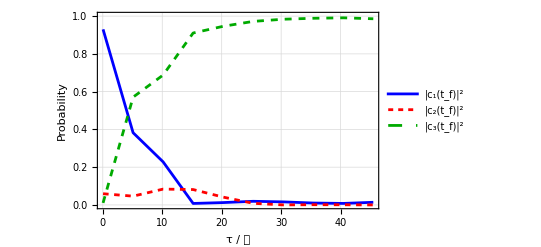

```mathematica
gBCM = Show[ListPlot[Transpose[{time,pBCM1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,pBCM2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,pBCM3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
```

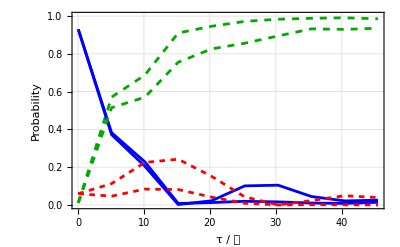

```mathematica
Show[gBCM,gLIN]
```

## Optimal time-averaged excess work

```mathematica
ProtOP = Table[NDSolve[{(1+ΩpOP[t]^2) (1+3 ΩpOP[t]^2+3 ΩpOP[t]^4+ΩpOP[t]^6-12 ΩpOP'[t]^2) (-3 ΩpOP[t] ΩpOP'[t]^2+ΩpOP''[t]+ΩpOP[t]^2 ΩpOP''[t])==0, ΩpOP[ti]==Ωpi, ΩpOP[tf]==Ωpf},ΩpOP[t],{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}}}

## Optimal Zheng-2 energetic cost

```mathematica
ProtZh=Table[NDSolve[{ΩpZh''[t]==(2 ΩpZh[t] ΩpZh'[t]^2)/(1+ΩpZh[t]^2), ΩpZh[ti]==Ωpi, ΩpZh[tf]==Ωpf},ΩpZh[t],{t,ti,tf}], {tf,Tmin,Tmax,ΔT}]
```

{{{ΩpZh[t]→InterpolatingFunction[…][t]}},{{ΩpZh[t]→InterpolatingFunction[…][t]}},{{ΩpZh[t]→InterpolatingFunction[…][t]}},{{ΩpZh[t]→InterpolatingFunction[…][t]}},{{ΩpZh[t]→InterpolatingFunction[…][t]}},{{ΩpZh[t]→InterpolatingFunction[…][t]}},{{ΩpZh[t]→InterpolatingFunction[…][t]}},{{ΩpZh[t]→InterpolatingFunction[…][t]}},{{ΩpZh[t]→InterpolatingFunction[…][t]}},{{ΩpZh[t]→InterpolatingFunction[…][t]}}}

```mathematica
SolZh = Table[NDSolve[{ⅈ*ℏ*c1Zh'[t] ==(ℏ/2)*Evaluate[ΩpZh[t]/.Flatten[Part[ProtZh,(tf-Tmin)/ΔT + 1]]]*c2Zh[t],ⅈ*ℏ*c2Zh'[t] ==(ℏ/2)*Evaluate[ΩpZh[t]/.Flatten[Part[ProtZh,(tf-Tmin)/ΔT + 1]]]*c1Zh[t]+(ℏ/2)*Δ*c2Zh[t]+ (ℏ/2)*Ωs[t]*c3Zh[t],ⅈ*ℏ*c3Zh'[t] ==+(ℏ/2)*Ωs[t]*c2Zh[t],c1Zh[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωpi^2 ],c2Zh[ti]==0,c3Zh[ti]==-Ωpi/Sqrt[Ωs[ti]^2 + Ωpi^2 ] },{c1Zh,c2Zh,c3Zh},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}},{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}},{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}},{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}},{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}},{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}},{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}},{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}},{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}},{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}}}

```mathematica
pZh1 = Table[Abs[c1Zh[t]/.Part[Flatten[Part[SolZh,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pZh2 = Table[Abs[c2Zh[t]/.Part[Flatten[Part[SolZh,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pZh3 = Table[Abs[c3Zh[t]/.Part[Flatten[Part[SolZh,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
```

{0.983769,0.00237781,0.00401663,0.00597974,0.0109227,0.0131422,0.010645,0.00844005,0.0105052,0.0141831}

{0.00615585,0.0366585,0.000233043,0.00407834,0.00415225,0.00102403,0.0000466092,0.000945976,0.00100914,0.000231195}

{0.0100749,0.960964,0.99575,0.989942,0.984925,0.985834,0.989308,0.990614,0.988486,0.985586}

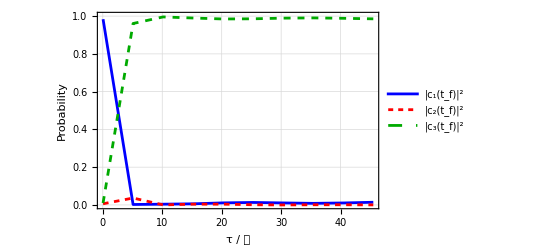

```mathematica
gZh = Show[ListPlot[Transpose[{time,pZh1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,pZh2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,pZh3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
```

## Uniform adiabatic

```mathematica
Integrate[x/((x^2+ a^2)*((x^2+a^2)^(1/2)+ 2* d)),x]
```

Log[√(a^2+x^2)]/(2 d)-Log[2 d^2+d √(a^2+x^2)]/(2 d)

```mathematica
f[x_,a_,d_]:= Log[√(a^2+x^2)]/(2 d)-Log[2 d^2+d √(a^2+x^2)]/(2 d)
```

```mathematica
c[tf_] := 2*(f[Ωpf,Ωs[ti],Δ] -  f[Ωpi,Ωs[ti],Δ])/tf
```

```mathematica
(*ProtUA = Table[NDSolve[{D[ΩpUA[t]*ΩpUA'[t]/((ΩpUA[t]^2 + Ωs[t]^2)*((ΩpUA[t]^2 + Ωs[t]^2)^(1/2)- 2*Δ)),t] ==0 , ΩpUA[ti]==Ωpi, ΩpUA[tf]==Ωpf},ΩpUA,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]*)
ProtUA = Table[NDSolve[{ΩpUA[t]*ΩpUA'[t]/((ΩpUA[t]^2 + Ωs[t]^2)*((ΩpUA[t]^2 + Ωs[t]^2)^(1/2)+ 2*Δ))==c[tf]/2 , ΩpUA[ti]==Ωpi},ΩpUA,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{ΩpUA→InterpolatingFunction[…]}},{{ΩpUA→InterpolatingFunction[…]}},{{ΩpUA→InterpolatingFunction[…]}},{{ΩpUA→InterpolatingFunction[…]}},{{ΩpUA→InterpolatingFunction[…]}},{{ΩpUA→InterpolatingFunction[…]}},{{ΩpUA→InterpolatingFunction[…]}},{{ΩpUA→InterpolatingFunction[…]}},{{ΩpUA→InterpolatingFunction[…]}},{{ΩpUA→InterpolatingFunction[…]}}}

```mathematica
SolUA = Table[NDSolve[{ⅈ*ℏ*c1UA'[t] ==(ℏ/2)*Evaluate[ΩpUA[t]/.Flatten[Part[ProtUA,(tf-Tmin)/ΔT + 1]]]*c2UA[t],ⅈ*ℏ*c2UA'[t] ==(ℏ/2)*Evaluate[ΩpUA[t]/.Flatten[Part[ProtUA,(tf-Tmin)/ΔT + 1]]]*c1UA[t]+(ℏ/2)*Δ*c2UA[t]+ (ℏ/2)*Ωs[t]*c3UA[t],ⅈ*ℏ*c3UA'[t] ==+(ℏ/2)*Ωs[t]*c2UA[t],c1UA[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωpi^2 ],c2UA[ti]==0,c3UA[ti]==-Ωpi/Sqrt[Ωs[ti]^2 + Ωpi^2 ] },{c1UA,c2UA,c3UA},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}},{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}},{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}},{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}},{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}},{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}},{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}},{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}},{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}},{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}}}

```mathematica
pUA1 = Table[Abs[c1UA[t]/.Part[Flatten[Part[SolUA,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pUA2 = Table[Abs[c2UA[t]/.Part[Flatten[Part[SolUA,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pUA3 = Table[Abs[c3UA[t]/.Part[Flatten[Part[SolUA,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
```

{0.977656,0.015773,0.0392834,0.0634379,0.0160998,0.0288726,0.0200057,0.0101563,0.0370108,0.00324616}

{0.0121521,0.193216,0.0105409,0.02201,0.0381466,0.00325029,0.0098894,0.0182777,0.00214786,0.00549171}

{0.0101919,0.79101,0.950175,0.914552,0.945754,0.967877,0.970104,0.971566,0.960842,0.991262}

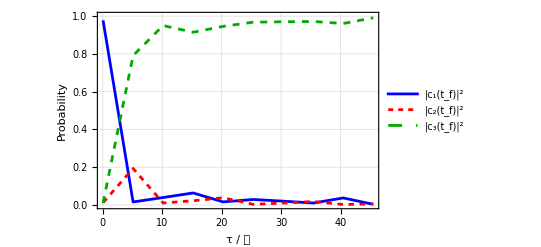

```mathematica
gUA = Show[ListPlot[Transpose[{time,pUA1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,pUA2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,pUA3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
```

## Local adiabatic

```mathematica
ProtLA = Table[NDSolve[{D[ΩpLA'[t]/((ΩpLA[t]^2 + Ωs[t]^2)*(1+ 2*Δ/(ΩpLA[t]^2 + Ωs[t]^2)^(1/2))),t] ==0 , ΩpLA[ti]==Ωpi, ΩpLA[tf]==Ωpf},ΩpLA,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{ΩpLA→InterpolatingFunction[…]}},{{ΩpLA→InterpolatingFunction[…]}},{{ΩpLA→InterpolatingFunction[…]}},{{ΩpLA→InterpolatingFunction[…]}},{{ΩpLA→InterpolatingFunction[…]}},{{ΩpLA→InterpolatingFunction[…]}},{{ΩpLA→InterpolatingFunction[…]}},{{ΩpLA→InterpolatingFunction[…]}},{{ΩpLA→InterpolatingFunction[…]}},{{ΩpLA→InterpolatingFunction[…]}}}

```mathematica
SolLA = Table[NDSolve[{ⅈ*ℏ*c1LA'[t] ==(ℏ/2)*Evaluate[ΩpLA[t]/.Flatten[Part[ProtLA,(tf-Tmin)/ΔT + 1]]]*c2LA[t],ⅈ*ℏ*c2LA'[t] ==(ℏ/2)*Evaluate[ΩpLA[t]/.Flatten[Part[ProtLA,(tf-Tmin)/ΔT + 1]]]*c1LA[t]+(ℏ/2)*Δ*c2LA[t]+ (ℏ/2)*Ωs[t]*c3LA[t],ⅈ*ℏ*c3LA'[t] ==+(ℏ/2)*Ωs[t]*c2LA[t],c1LA[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωpi^2 ],c2LA[ti]==0,c3LA[ti]==-Ωpi/Sqrt[Ωs[ti]^2 + Ωpi^2 ] },{c1LA,c2LA,c3LA},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}},{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}},{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}},{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}},{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}},{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}},{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}},{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}},{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}},{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}}}

```mathematica
pLA1 = Table[Abs[c1LA[t]/.Part[Flatten[Part[SolLA,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pLA2 = Table[Abs[c2LA[t]/.Part[Flatten[Part[SolLA,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pLA3 = Table[Abs[c3LA[t]/.Part[Flatten[Part[SolLA,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
```

{0.983106,0.00225994,0.0017978,0.00504907,0.00830097,0.0106249,0.0115018,0.0109083,0.00929963,0.00743284}

{0.00680801,0.0619961,0.00853483,0.00098126,0.000128777,0.000737124,0.00126558,0.00128471,0.00089462,0.000400716}

{0.010086,0.935744,0.989667,0.993969,0.99157,0.988638,0.987233,0.987807,0.989806,0.992166}

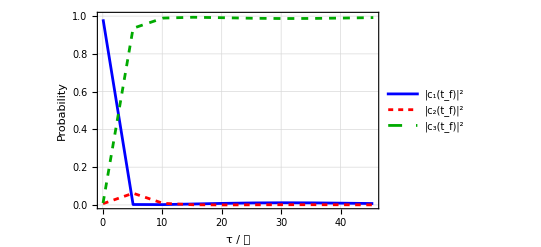

```mathematica
gLA = Show[ListPlot[Transpose[{time,pLA1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,pLA2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,pLA3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
```

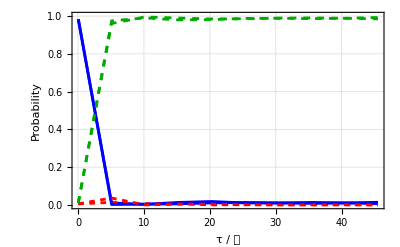

```mathematica
Show[gMA, gZh]
```

## Optimal Santos/Sarandy

```mathematica
Ωmax = 0.1
ProtSa =Table[ NDSolve[{(ΩpSa[t] ((1+ΩpSa[t]^2/(1+ΩpSa[t]^2/Ωmax^2))^3+8 (ΩpSa'[t])^2))/(√(1+ΩpSa[t]^2/Ωmax^2) (1+ΩpSa[t]^2/(1+ΩpSa[t]^2/Ωmax^2)))==4*ΩpSa''[t], ΩpSa[ti]==Ωpi, ΩpSa[tf]==Ωpf},ΩpSa[t],{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

0.1

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolve::berr: The scaled boundary value residual error of 4.58437×10^6 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolve::berr: The scaled boundary value residual error of 8.94825×10^6 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

NDSolve::berr: The scaled boundary value residual error of 9.43276×10^6 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

General::stop: Further output of NDSolve::berr will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,1.05367×10^-8}.

{{{ΩpSa[t]→InterpolatingFunction[…][t]}},{{ΩpSa[t]→InterpolatingFunction[…][t]}},{{ΩpSa[t]→InterpolatingFunction[…][t]}},{{ΩpSa[t]→InterpolatingFunction[…][t]}},{{ΩpSa[t]→InterpolatingFunction[…][t]}},{{ΩpSa[t]→InterpolatingFunction[…][t]}},{{ΩpSa[t]→InterpolatingFunction[…][t]}},{{ΩpSa[t]→InterpolatingFunction[…][t]}},{{ΩpSa[t]→InterpolatingFunction[…][t]}},{{ΩpSa[t]→InterpolatingFunction[…][t]}}}

```mathematica
SolSa = Table[NDSolve[{ⅈ*ℏ*c1Sa'[t] ==(ℏ/2)*Evaluate[ΩpSa[t]/.Flatten[Part[ProtSa,(tf-Tmin)/ΔT + 1]]]*c2Sa[t],ⅈ*ℏ*c2Sa'[t] ==(ℏ/2)*Evaluate[ΩpSa[t]/.Flatten[Part[ProtSa,(tf-Tmin)/ΔT + 1]]]*c1Sa[t]+(ℏ/2)*Δ*c2Sa[t]+ (ℏ/2)*Ωs[t]*c3Sa[t],ⅈ*ℏ*c3Sa'[t] ==+(ℏ/2)*Ωs[t]*c2Sa[t],c1Sa[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωpi^2 ],c2Sa[ti]==0,c3Sa[ti]==-Ωpi/Sqrt[Ωs[ti]^2 + Ωpi^2 ] },{c1Sa,c2Sa,c3Sa},{t,ti,tf}],{tf,Tmin, Tmax-4*ΔT, ΔT}]
```

{{{c1Sa→InterpolatingFunction[…],c2Sa→InterpolatingFunction[…],c3Sa→InterpolatingFunction[…]}},{{c1Sa→InterpolatingFunction[…],c2Sa→InterpolatingFunction[…],c3Sa→InterpolatingFunction[…]}},{{c1Sa→InterpolatingFunction[…],c2Sa→InterpolatingFunction[…],c3Sa→InterpolatingFunction[…]}},{{c1Sa→InterpolatingFunction[…],c2Sa→InterpolatingFunction[…],c3Sa→InterpolatingFunction[…]}},{{c1Sa→InterpolatingFunction[…],c2Sa→InterpolatingFunction[…],c3Sa→InterpolatingFunction[…]}},{{c1Sa→InterpolatingFunction[…],c2Sa→InterpolatingFunction[…],c3Sa→InterpolatingFunction[…]}}}

```mathematica
pSa1 = Table[Abs[c1Sa[t]/.Part[Flatten[Part[SolSa,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax-4*ΔT,ΔT}]
pSa2 = Table[Abs[c2Sa[t]/.Part[Flatten[Part[SolSa,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax-4*ΔT,ΔT}]
pSa3 = Table[Abs[c3Sa[t]/.Part[Flatten[Part[SolSa,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax-4*ΔT,ΔT}]
```

{0.960804,0.382663,0.0273731,0.0573607,0.0629791,0.0489343}

{0.0288038,0.00779688,0.0312673,0.0290399,0.0204522,0.0124416}

{0.0103923,0.609539,0.941359,0.913599,0.916569,0.938624}

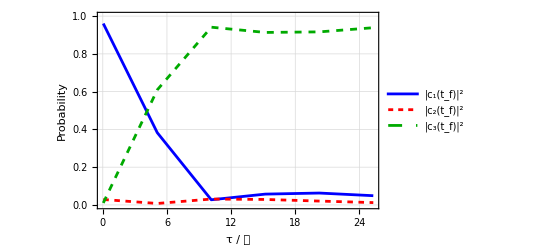

```mathematica
gSa = Show[ListPlot[Transpose[{time2,pSa1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time2,pSa2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time2,pSa3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
```

## Protocols

6

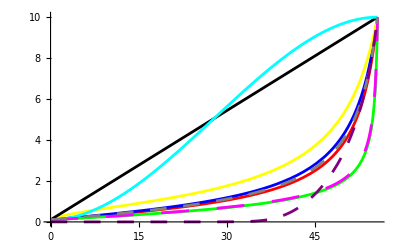

```mathematica
n = 6
Show[Plot[Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,n]]],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->Red], Plot[Evaluate[ΩpLA[t]/.Flatten[Part[ProtLA,n]]],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->Blue],Plot[Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,n]]],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->Green], 
Plot[Evaluate[ΩpUA[t]/.Flatten[Part[ProtUA,n]]],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->Yellow], 
Plot[Ωp[t, (n-1)*ΔT + Tmin],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->Black], 
Plot[ΩpBCM[t, (n-1)*ΔT + Tmin],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->Cyan], 
Plot[Evaluate[ΩpOP[t]/.Flatten[Part[ProtOP,n]]],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->{Magenta, Dashing[0.05]}], 
Plot[Evaluate[ΩpZh[t]/.Flatten[Part[ProtZh,n]]],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->{Gray, Dashing[0.03]}],
Plot[Evaluate[ΩpSa[t]/.Flatten[Part[ProtSa,n]]],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->{Purple, Dashing[0.03]}]]
```

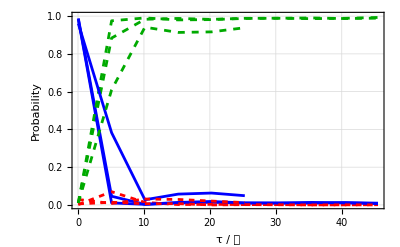

```mathematica
Show[gFQ,gMA, gSa]
```

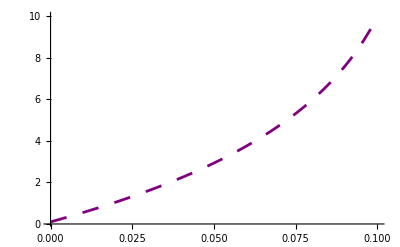
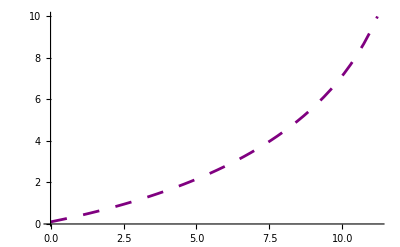
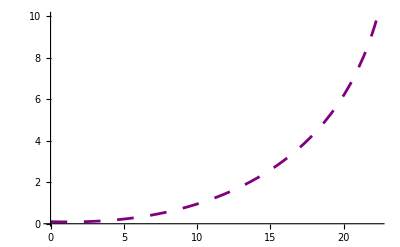
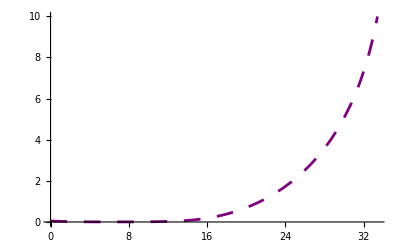
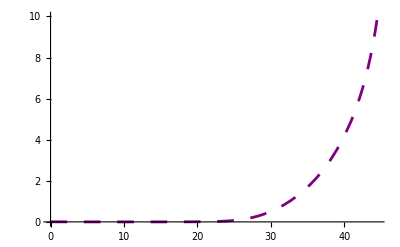
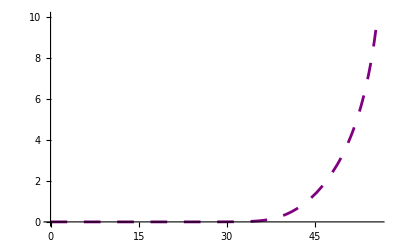
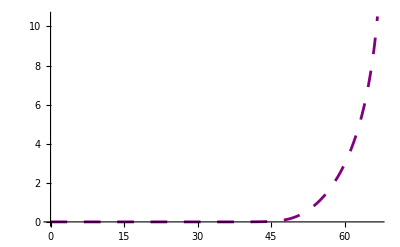
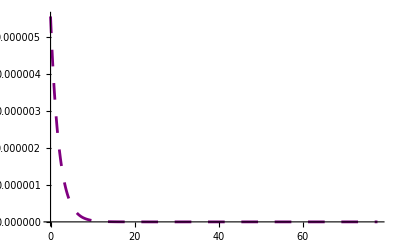

```mathematica
Table[Plot[Evaluate[ΩpSa[t]/.Flatten[Part[ProtSa,n]]],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->{Purple, Dashing[0.03]}],{n,1,m}]
```